```mathematica
dof[m_,n_]:=Simplify[(n(n-1)/2)-((n-m)(n-m-1)/2)]
```

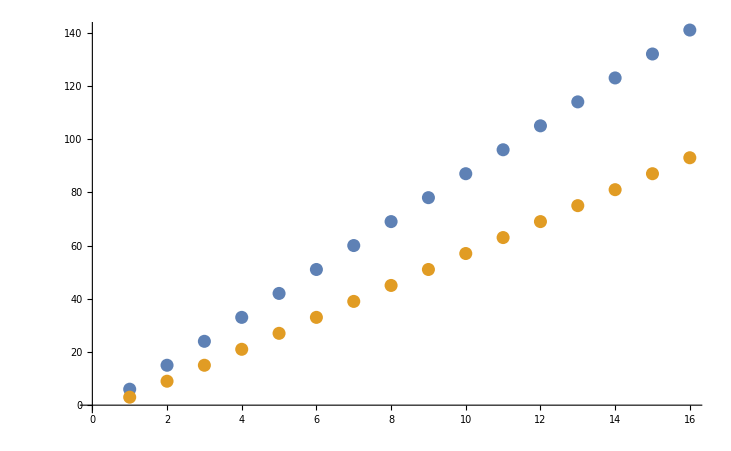

```mathematica
ListPlot[{Table[dof[3,n],{n,4,50,3}],Table[dof[3,n]-(n-1),{n,4,50,3}]}]
```

```mathematica
Collect[dof[m,n],n]
```

-1/2 m (1+m)+m n

```mathematica
Collect[Simplify[dof[m,n]-(n-1)],n]
```

-1/2 (-1+m) (2+m)+(-1+m) n

```mathematica
Collect[Simplify[dof[3,n]],n]
```

-6+3 n

```mathematica
Collect[Simplify[dof[3,n]-(n-1)],n]
```

-5+2 n

```mathematica
Table[{n,dof[3,n],dof[3,n]-(n-1)},{n,4,50,3}]//MatrixForm
```

(4 | 6 | 3
7 | 15 | 9
10 | 24 | 15
13 | 33 | 21
16 | 42 | 27
19 | 51 | 33
22 | 60 | 39
25 | 69 | 45
28 | 78 | 51
31 | 87 | 57
34 | 96 | 63
37 | 105 | 69
40 | 114 | 75
43 | 123 | 81
46 | 132 | 87
49 | 141 | 93)

```mathematica
rot[t_,i_,j_,n_]:=Module[{mm,tt},(mm=IdentityMatrix[n];
ToExpression[StringJoin[ToString[tt],"=",ToString[t],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=Cos[tt];mm[[i,j]]=-Sin[tt];mm[[j,i]]=Sin[tt];mm[[j,j]]=Cos[tt];mm)]
```

```mathematica
rot[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[x[2,3]] | -Sin[x[2,3]] | 0
0 | Sin[x[2,3]] | Cos[x[2,3]] | 0
0 | 0 | 0 | 1)

```mathematica
rot2[x_,i_,j_,n_]:=Module[{mm,xx},(mm=IdentityMatrix[n];
ToExpression[StringJoin[ToString[xx],"=",ToString[x],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=Sqrt[1-xx];mm[[i,j]]=-Sqrt[xx];mm[[j,i]]=Sqrt[xx];mm[[j,j]]=Sqrt[1-xx];mm)]
```

```mathematica
rot2[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | √(1-x[2,3]) | -√x[2,3] | 0
0 | √x[2,3] | √(1-x[2,3]) | 0
0 | 0 | 0 | 1)

```mathematica
fullRotMat[t_,m_,n_]:=Module[{mm},(mm=IdentityMatrix[n];For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,If[i<=m||j<=m,mm=mm.rot[t,i,j,n],Nothing]]];mm)]
```

```mathematica
fullRotMat[t,1,3]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | -Sin[t[1,2]] | -Cos[t[1,2]] Sin[t[1,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] | -Sin[t[1,2]] Sin[t[1,3]]
Sin[t[1,3]] | 0 | Cos[t[1,3]])

```mathematica
fullRotMat2[x_,m_,n_]:=Module[{mm},(mm=IdentityMatrix[n];For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,If[i<=m||j<=m,mm=mm.rot2[x,i,j,n],Nothing]]];mm)]
```

```mathematica
fullRotMat2[t,1,3]//MatrixForm
```

(√(1-t[1,2]) √(1-t[1,3]) | -√t[1,2] | -√(1-t[1,2]) √t[1,3]
√t[1,2] √(1-t[1,3]) | √(1-t[1,2]) | -√t[1,2] √t[1,3]
√t[1,3] | 0 | √(1-t[1,3]))

```mathematica
sumRows[mm_,m_,n_]:=Table[Sum[Map[Abs,mm][[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
makeEqn[ms_,n_]:=Table[o==ms[[i]],{i,1,n}]
```

```mathematica
trySolve[mm_,x_,xmin_,xmax_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
mms=sumRows[mmm,m,n];
mme=makeEqn[mms,n];
Solve[Join[mme,{0<=o<=1},makeCon[x,m,n,xmin,xmax]],Reals]
)]
```

```mathematica
Table[{2,n,dof[2,n],dof[2,n]-(n-1)},{n,3,5,2}]//MatrixForm
```

(2 | 3 | 3 | 1
2 | 5 | 7 | 3)

```mathematica
Table[{3,n,dof[3,n],dof[3,n]-(n-1)},{n,5,5,3}]//MatrixForm
```

(3 | 5 | 9 | 5)

```mathematica
sumRowsNoAbs[mm_,m_,n_]:=Table[Sum[mm[[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
trySolveNoAbs[mm_,x_,xmin_,xmax_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
mms=sumRowsNoAbs[mmm,m,n];
mme=makeEqn[mms,n];
Solve[Join[mme,{0<=o<=1},makeCon[x,m,n,xmin,xmax]],Reals]
)]
```

```mathematica
makeSub[t_,x_,m_,n_]:=Flatten[Table[Table[{Sin[t[i,j]]->Sqrt[x[i,j]],Cos[t[i,j]]->Sqrt[1-x[i,j]]},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeCon[x_,m_,n_,xmin_,xmax_]:=Flatten[Table[Table[{xmin<=x[i,j]<=xmax},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeCon[x,2,3,0,1]
```

{0≤x[1,2]≤1,0≤x[1,3]≤1,0≤x[2,3]≤1}

```mathematica
makeCon[t,2,3,0,2Pi]
```

{0≤t[1,2]≤2 π,0≤t[1,3]≤2 π,0≤t[2,3]≤2 π}